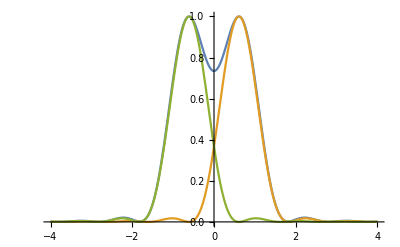

```mathematica
diff=0.61;
Plot[{((2BesselJ[1, (x+diff)*Pi])/((x+diff)*Pi))^2}, {x, -4, 4}, PlotRange->{{-4,4},{0,1}} ]
```

```mathematica
eps=10^-6;
domainY=3;
domainX=4;
samples=40;
major=8;
i[x_, y_]:= ((2BesselJ[1, √(x^2+y^2)*Pi+eps])/(√(x^2+y^2)*Pi+eps))^2;
createData[distance_]:=Flatten[Table[Join[Table[{N[x,3] ,N[y,3],SetPrecision[i[x+distance/2, y]+i[x-distance/2,y],3] }, {x, -domainX, domainX, domainX/samples}],{{}}], {y, domainY, -domainY, -domainY/samples}],1];
dataAll=createData[1.22];
data = Join[{{"x", "y" ,"I"}}, dataAll]

(*dataY=
Join[
{{"x", "y" ,"I"}},Flatten[
Table[
Join[
Table[
{N[x,3] ,N[y,3],i[x+0.61, y]+i[x-0.61,y] }, {x, -domainX, domainX, domainX/samples}
],{{}}
], {y, -domainY, domainY, domainY/major }
],1
]
];*)
dataY=
Join[
{{"x", "y" ,"I"}},
Table[
{N[x,3] ,0,i[x+0.61, 0]+i[x-0.61,0] }, {x, -domainX, domainX, domainX/samples}
]];

(*dataX=Join[{{"x", "y" ,"I"}}, Flatten[Table[Join[Table[{N[x,3],N[y,3],i[x+0.61, y]+i[x-0.61,y] }, {y, -domainY, domainY, domainY/samples}],{{}}], {x, -domainX, domainX,domainX/major }],1]];*)
dataX=Join[{{"x", "y" ,"I"}}, Table[{0.61,N[y,3],N[i[1.22, y]+i[0,y],3] }, {y, -domainY, domainY, domainY/samples}]];

Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk.txt"}], data, "Table"];
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-y.txt"}], dataY, "Table"];
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-x.txt"}], 
dataX, "Table"];
```

{{x,y,I},{-4.,3.,0.000799},{-3.9,3.,0.000492},{-3.8,3.,0.000215},6635,{3.8,-3.,0.000215},{3.9,-3.,0.000492},{4.,-3.,0.000799},{}}
 |  |  |  |

```mathematica
createData[distance_]:=Flatten[Table[Table[{N[x,3] ,N[y,3],i[x+distance/2, y]+i[x-distance/2,y] }, {x, -domainX, domainX, 0.1}], {y, domainY, -domainY, -0.1}],1];
Table[Export[FileNameJoin[{NotebookDirectory[],"..","img","eiry-disk-"<>ToString[d]<>".png"}],
ListDensityPlot[createData[1.22*d], ColorFunction->GrayLevel,Frame->None, AspectRatio->3/4, ImageSize->800],"Image"] ,{d, 1, 3}];
```

Options::optnf: ImageResolution is not a known option for Graphics.

General::stop: Further output of Options::optnf will be suppressed during this calculation.

```mathematica
eiry[x_,diff_]:=((2BesselJ[1, (x-0.61diff)*Pi+eps])/((x-0.61diff)*Pi+eps))^2+((2BesselJ[1, (x+0.61diff)*Pi+eps])/((x+0.61diff)*Pi+eps))^2;
data=Table[Join[{x, ((2BesselJ[1, x*Pi+eps])/(x*Pi+eps))^2},Table[eiry[x,d],{d,1,3,1}]],{x,-4,4,0.1}];
Export[FileNameJoin[{NotebookDirectory[],"..","data","eiry-disk-profile.txt"}],Join[{{"x", "e0","e1","e2","e3"}},data],"Table"];
```